# Chapter. Finite difference methods

Mathematica 	Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[NDSolve::"mxsst"];
Off[NDSolve::"bdisc"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->17,

PageHeaders-> {
{Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12], Cell[TextData[{"Finite Difference Methods"}], FontFamily->"Arial",FontSize->12],None}, 
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Explicit Finite Difference Methods","Dimensionless variables","Initial condition and boundary conditions","Explicit Solution with Mathematica","Implicit Finite Difference Methods","Implicit Solution with Mathematica","Summary","Further Reading"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
SetOptions[Plot,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize-> 288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListPlot,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->Directive[AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListLogPlot,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
ImageSize->400,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->Directive[Black,AbsolutePointSize[4.5]],
Joined->False];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
Axes->True,
AxesLabel->{"k","j","  c"},
AxesEdge->{{1,-1},{-1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2,-.5,1}];
```

```mathematica
SetOptions[Plot3D,
AspectRatio-> 1,
PlotRange->All,
PlotPoints->40,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Mesh-> False,
ViewPoint-> {-2.360, 3.580, 2.000}];
```

```mathematica
Clear[ticks1,ticks2];

(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
options1={
Frame->True,
Axes->False,
PlotRange->{{0,1100},{-2,1.5}},
FrameLabel->{"n","t",None,None},RotateLabel->False};
```

```mathematica
options2={
 Frame->{True,True,False,False},
FrameLabel-> {"n","t",None,None},
PlotStyle-> {AbsolutePointSize[7]},
PlotMarkers->{★,•,◼,◆},
RotateLabel-> False};
```

```mathematica
$Line=0;
```

Cell[TextData[{
 
 CounterBox["Chapter"],
 ".",
 
 CounterBox["Section"],
 " Introduction"
}], "SectionFirst",
 CellTags->"s3.1"]

In the previous chapter methods of finding analytical solutions to PDEs were discussed. Many problems in electrochemistry are such that no analytical solution exists. In these cases numerical solutions are required. One method of numerical solution is to use the Mathematica function NDSolve although problems may arise due to the discontinuity in the boundary conditions that exist in electrochemical problems. This error message can be switched off prior to using NDSolve. The problem is set up by entering the partial differential equation and the boundary conditions. The result is an interpolating function. For example for a potential step to the limiting current region the problem could be solves as demonstrated below:

```mathematica
Off[NDSolve::"bdisc"];
ClearAll[c,result];

result=c/.First[NDSolve[{D[c[x,t],t]==D[c[x,t],{x,2}],c[x,0]==If[x>0,1,0],c[0,t]==0,c[1,t]==1},c,{x,0,1},{t,0,.05},MaxSteps-> 200]]
```

InterpolatingFunction[{{0.,1.},{0.,0.05}},<>]

```mathematica
Plot3D[result[x,t],{x,0,1},{t,0,.05}]
```

-Graphics3D-

Fig. Chapter.FigureCaption  NDSolve solution of the concentration profile for a potential step experiment.

The current is proportional to (∂c(x, t)/∂x)_(x=0) therefore taking the derivative of the result at x=0 gives a plot proportional to the current. In this example the condition x=0 is made using a rule replacement.

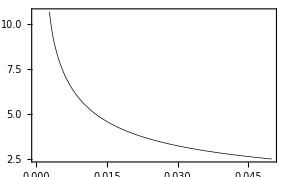

```mathematica
Plot[Evaluate[D[result[x,t],x]/.x->0],{t,0,.05},
FrameTicks-> {Automatic,None,Automatic,None}]
```

Fig. Chapter.FigureCaption  NDSolve solution of the current for a potential step experiment.

Unfortunately NDSolve is fairly restrictive in the types of PDEs that can be solved. Another numerical method for solving PDEs is the finite difference method. Finite difference methods can be divided into three types: explicit methods, implicit methods and a combination of explicit and implicit methods. In this chapter explicit and implicit methods will be defined and methods to write finite difference expressions for typical partial differential equations encountered in electrochemistry and use Mathematica to solve these finite difference equations will be described.

## Chapter.Section Explicit Finite Difference Methods

Using finite difference methods we will seek to determine the gradient at a particular point on a curve by discretizing the points surrounding it as shown below in Fig. Chapter.FigureCaption.

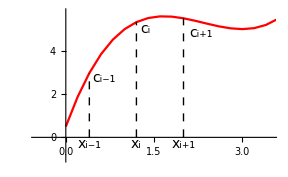

```mathematica
ClearAll[label,option1,somePoints,x,c];

label[x_]:=DisplayForm[TraditionalForm[MakeBoxes[Style[x,14],TraditionalForm]]];

option1={
Axes->{True,True},
AxesOrigin->{0,0},
Frame->False,
Joined->True,
ImagePadding->{{5,5},{5,5}},
PlotRange->{{-0.5,3.5},{-1,5.8}},
PlotStyle-> RGBColor[1,0,0],
Ticks->False, 
Epilog->{
Dashing[{0.02,0.02}],
Line[{{2.,0},{2,5.5}}],
Line[{{1.2,0},{1.2,5.324}}],
Line[{{0.4,0},{0.4,2.972}}],
Text[label[Subscript[x, i-1]],{0.4,-0.3}],
Text[label[Subscript[x, i]],{1.2,-0.3}],
Text[label[Subscript[x, i+1]],{2.,-0.3}],
Text[label[Subscript[c, i-1]],{0.65,2.75}],
Text[label[Subscript[c, i]],{1.35,5.}],
Text[label[Subscript[c, i+1]],{2.3,4.8}]
}
};

somePoints=Table[{x+1,0.5 x^3-2 x^2+2 x+5},{x,-1,3.5,0.2}];

plot1=ListPlot[somePoints,option1]
SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],Next,Cell]
```

Fig. Chapter.FigureCaption  Discretization of a function.

Taking Fick’s second law

(∂c(x, t))/(∂t)=D(∂^2 c(x, t))/(∂x^2)

the Taylor series expansion (see Appendix 1) can be used to arrive at a numerical expression. Fick’s second law can re-written in finite difference form as

lim_(t → 0) (c(x, t+Δt)-c(x, t))/Δt=D lim_(x → 0) ([c(x+Δx, t)-c(x, t)]-[c(x, t)-c(x-Δx, t)])/(Δx)^2

If we assume that we can obtain sufficient accuracy by using sufficiently small enough time and distance steps we can discretize Fick’s second law as shown below:

c(x, t+Δt)-c(x, t)=DΔt/(Δx)^2[c(x+Δx, t)-2c(x, t)+c(x-Δx, t)]

The order of the error can be estimated in this approximation from the Taylor series expansion (see Appendix 1). Truncating the Taylor series at the first time derivative we have

```mathematica
ClearAll[t,Δt];

exp1=Series[c[t+Δt],{Δt,0,1}]
```

c[t]+c'[t] Δt+O[Δt]^2

Rearranging the output gives

c'( t)=(c( t+Δt)-c( t))/Δt-(𝒪( (Δ t)^2))/Δt

Therefore the error for the approximation of the time derivative is 𝒪(Δ t). Expanding c(x+Δx) and truncating at the third derivative we have

```mathematica
ClearAll[x,Δx];

exp2=Series[c[x+Δx],{Δx,0,3}]
```

c[x]+c'[x] Δx+1/2 c''[x] Δx^2+1/6 c^(3)[x] Δx^3+O[Δx]^4

so that c( x+Δ x) is:

c( x+Δx)=c( x)+Δxc'( x)+((Δx)^2 c''( x))/2+((Δx)^3 c'''( x))/6+𝒪( (Δ x)^4)

Expanding c(x-Δx) and truncating at the third derivative we have

```mathematica
ClearAll[x,Δx];

exp3=Series[c[x-Δx],{Δx,0,3}]
```

c[x]-c'[x] Δx+1/2 c''[x] Δx^2-1/6 c^(3)[x] Δx^3+O[Δx]^4

Therefore c( x+Δ x) can be written as:

c( x-Δx)=c( x)-Δxc'( x)+((Δx)^2 c''( x))/2-((Δx)^3 c'''( x))/6+𝒪( (Δ x)^4)

Applying the function Normal to eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered), in order to remove the remainder, and adding them together and solving for c''(x) gives

```mathematica
Solve[{c[x+Δx]+c[x-Δx]== Normal[exp2]+ Normal[exp3]},c''[x]]
```

{{c''[x]→(-2 c[x]+c[x-Δx]+c[x+Δx])/Δx^2}}

The error for the approximation of the second space derivative is 𝒪((Δx)^2) which is obtained by dividing 𝒪( (Δ x)^4) by (Δx)^2. By dividing time and distance into discrete increments of fixed size a concentration grid is created (Fig. Chapter.FigureCaption).

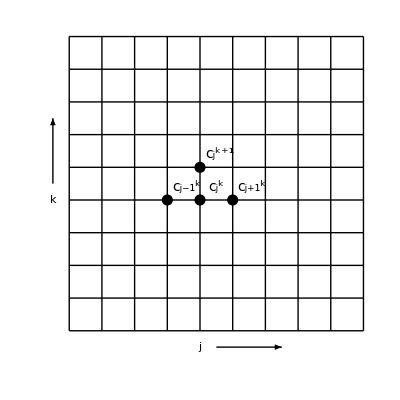

```mathematica
ClearAll[vertical,horizontal,option2];

vertical=Table[Line[{{i,1},{i,10}}],{i,1,10}];
horizontal=Table[Line[{{1,i},{10,i}}],{i,1,10}];

option2={
AspectRatio-> 1,
ImagePadding->{{5,5},{5,5}},
PlotRange->{{0,10},{0,10}},
Prolog-> {
Text[TraditionalForm[k],{0.5,5.}],
Text[TraditionalForm[j],{5.,0.5}],
Text[label[Subscript[c, j]^k],{5.5,5.4}],
Text[label[Subscript[c, j]^(k+1)],{5.6,6.4}],
Text[label[Subscript[c, j-1]^k],{4.6,5.4}],
Text[label[Subscript[c, j+1]^k],{6.6,5.4}],
PointSize[0.02],
Point[{4,5}],
Point[{5,5}],
Point[{6,5}],
Point[{5,6}],
Arrowheads[{0,0.03}],
Arrow[{{0.5,5.5},{0.5,7.5}}],
Arrow[{{5.5,0.5},{7.5,0.5}}]
}
};

Graphics[{vertical,horizontal},option2]
SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Grid showing concentration at grid coordinates j and k.

In this way distance and time can then be indexed. For example the distance in the x direction from the electrode surface can be divided into (m-1) increments of size Δ x. The distance at any point x from the electrode surface can be considered to be equal to the jth increment. Therefore a distance (x+Δx) from the surface will be equal to the (j+1)th increment and any distance (x-Δx) from the surface will be equal to the (j-1)th increment. We use (m-1) increments rather than m increments because the first point on the grid, j=1, corresponds to x=0. Likewise time, t, can be divided into (n-1) increments of size Δt with time, t, being the kth increment, (t+Δt) the (k+1)th increment, and (t-Δt) the (k-1)th increment. The first point on the grid, k=1, corresponds to t=0.
Returning now to the discretized version of eqn (Chapter.EquationNumbered) this can be expressed in terms of the points on the grid as

c(j, k+1)=c(j, k)+DΔt/(Δx)^2(c(j+1, k)-2c(j,k)+c(j-1, k))

Using this equation the concentration at  t=k+1 can be determined from the previously calculated concentration at t=k. This form of finite difference method is called a fully explicit scheme.

## Chapter.Section Dimensionless variables

It is desirable to use dimensionless quantities when obtaining numerical solutions. By dividing the concentration terms by the bulk concentration a dimensionless concentration is obtained at each point j and k, for which we’ll use the notation c_j^k. Notice that the term DΔt/(Δx)^2 in eqn (Chapter.EquationNumbered) is also dimensionless. In the electrochemical literature this term is referred to as the model diffusion coefficient and generally given the symbol D.

D=DΔt/(Δx)^2

It can be shown that for the fully explicit finite difference method to be stable requires that D⩽0.5. Re-writing eqn (Chapter.EquationNumbered) in dimensionless terms gives

D c_(j-1)^k+(1-2D)c_j^k+D c_(j+1)^k=c_j^(k+1)

To obtain a dimensionless time, t, time t is divided by the duration of the experiment, t_n. The duration is defined as t_n=(n-1)Δt therefore

t(k)=t/t_n=((k-1)/(n-1))				1≤ k≤ n

To obtain the dimensionless distance, x, the distance, which is given by x=(j-1)Δ x, is divided by the quantity √Dt_n

x(j)=x/(D t_n)^(1/2)=((j-1)Δx)/(DΔt(n-1))^(1/2)

After substituting eqn (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) the expression for the dimensionless distance is

x(j)=(j-1)/(D(n-1))^(1/2)

We saw in §1.5.1 that the concentration profile following a potential step experiment is

c(x, t)=c^*erf(x/(2(D t)^(1/2)))

Since erf(3)≅1 it follows from eqn (Chapter.EquationNumbered) that when x/(2(Dt_n)^(1/2))=3 the concentration is c(x,t) ≅ c^*. Therefore the maximum distance from the electrode surface that needs to be considered is

x_max=(m-1)Δx=6(D t_n)^(1/2)

In dimensionless form means that (x(j))_max = 6. The maximum number of spacial grid points required will therefore be

(m-1)=6((D t_n)/(Δx)^2)^(1/2)=6(D(n-1))^(1/2)

To arrive at an expression for the dimensionless current we first consider the flux, J, which is

J(x,t)=-D(∂c(x,t))/(∂x)

This can re-written in forward difference form as

J(x,t)=-D/Δx(c(x+Δx,t)-c(x,t))

In terms of dimensionless concentrations eqn (Chapter.EquationNumbered) is

J(j,k) =-(D c^*)/Δx(c_(j+1)^k-c_j^k)

The current is defined as

i(t)=-nFA(D((∂c_O(x,t))/(∂x)))_(x=0)=nFAJ_O(0,t)

where subscript O indicates the oxidized species. Substituting eqn (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) gives the two point approximation for the current in terms of j and k indices

i(k) =-nFA c^*D/Δx(c_2^k-c_1^k)

Substituting Δ x=(D Δt/D)^(1/2) and Δ t=t_n/(n-1) into eqn (Chapter.EquationNumbered) gives the dimensionless current, i(k),

i(k) =(i(k))/(nFA c^*)(t_n/D)^(1/2)=-(c_2^k-c_1^k)(D(n-1))^(1/2)

A more accurate estimation of the current is obtained by using a higher order approximation for the concentration gradient at x=0 (see Appendix 1). The three point approximation for the flux at the surface is

J(1,k) =-Dc^*/(2Δx)(-3 c_1^k+4 c_2^k-c_3^k)

Substituting this expression into eqn (Chapter.EquationNumbered) gives

i(k) =nFAc^*D/(2Δx)(-3 c_1^k+4 c_2^k-c_3^k)

The three point approximation for the dimensionless current is therefore

i(k) =(-3 c_1^k+4 c_2^k-c_3^k)(D(n-1))^(1/2)/2

An expression for the dimensionless rate constant can be derived from the Butler-Volmer equation:

i(t)=n F A k_s(c_R_1(0,t)exp((1-α)(n F)/(R T)(E-E°'))-c_O_1(0,t)exp(-α(n F)/(R T)(E-E°')))

After making the concentrations dimensionless we have

(i(k))/(nFA c^*)=k_s(c_R_1^k exp((1-α)E)-c_O_1^k exp(-αE))

where E is the dimensionless potential

E=nF/RT(E-E°')

When eqn (Chapter.EquationNumbered) is compared to eqn (Chapter.EquationNumbered) we see that if eqn (Chapter.EquationNumbered) is multiplied by (t_n/D)^(1/2) the dimensionless current is obtained:

i(k) =(i(k))/nFAc^*(t_n/D)^(1/2)=(k_s(t_n/D))^(1/2)(c_R_1^k exp((1-α)E)-c_O_1^k exp(-αE))

Therefore since the terms within the parenthesis on the right hand side of eqn (Chapter.EquationNumbered) are already dimensionless the dimensionless rate constant is defined as

k_s=(k_s(t_n/D))^(1/2)

## Chapter.Section Initial condition and boundary conditions

Just as we needed two boundary conditions and an initial condition to solve the PDE analytically we also need these for the finite difference simulation. The initial condition and boundary conditions are typically

c(x,0)=c^*	for t=0

c(0,t)=f(t)	for t>0

c(∞,t)=c^*	for t>0

The representation of the initial and boundary values for finite difference methods are shown below in Fig. Chapter.FigureCaption.
In dimensionless form these conditions can be written as

c_j^1=1	for k=1

c_1^k=f(k)	for x=0, k>1

c_m^k=1	for x=6, k>1

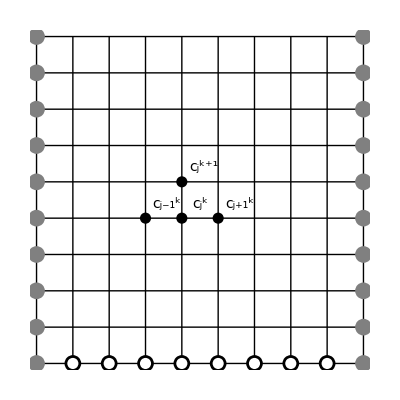

```mathematica
ClearAll[vert,horiz,leftBoundary,rightBoundary,initial,option3];

(*make lines*)
vert=Table[Line[{{i,1},{i,10}}],{i,1,10}];
horiz=Table[Line[{{1,i},{10,i}}],{i,1,10}];

(*make list of points*)
leftBoundary=Table[{1,i},{i,10}];
rightBoundary=Table[{10,i},{i,10}];
initial=Table[{i,1},{i,2,9}];

option3={
AspectRatio-> 1,
ImagePadding->{{5,5},{5,5}},
Epilog-> {
Text[label[Subscript[c, j]^k],{5.5,5.4}],
Text[label[Subscript[c, j]^(k+1)],
{5.6,6.4}],
Text[label[Subscript[c, j-1]^k],{4.6,5.4}],
Text[label[Subscript[c, j+1]^k],{6.6,5.4}],
PointSize[0.02],
Point[{4,5}],
Point[{5,5}],
Point[{6,5}],
Point[{5,6}],
PointSize[0.03],
Point/@initial,
GrayLevel[0.5],Point/@rightBoundary,Point/@leftBoundary,
GrayLevel[1],PointSize[0.02],Point/@initial
}
};

Graphics[{vert,horiz},option3]
SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell];
```

Fig. Chapter.FigureCaption  Grid for finite differencing with boundary conditions ● and initial condition ○.

## Chapter.Section Explicit Solution with Mathematica

Chapter.Section.Subsection Procedural method

Procedural methods have a similar form to programming languages such as FORTRAN. To perform a simple finite difference simulation in Mathematica we first create an x, t grid to represent the concentration at discrete points along the x and t axes as shown in Fig. Chapter.FigureCaption. Let m be the number of subintervals along the x axis, and n be the number of subintervals along the t axis. We’ll represent the dimensionless concentration c_j^k, as c⟦j,k⟧. For simplicity in this chapter we’ll consider the case of a potential step to the limiting current region in which the initial condition is given by eqn (Chapter.EquationNumbered) and the boundary conditions are given by eqn (Chapter.EquationNumbered) and

c_1^k=0	for  k>1

We begin by using the Table function to create an n×m matrix, which for the finite difference method we’ll refer to as a grid. The term ‘mesh’ is also frequently used in the literature instead of grid. The variables m and n are defined as integers. By doing this if non integer values are inadvertently entered the calculation will not be attempted.

```mathematica
ClearAll[makeGrid];

makeGrid[m_Integer,n_Integer]:=Module[{j,k,c},
		
c=Table[1.,{m},{n}];(*define initial condition*)
		For[j=1,j≤m,j++,c⟦j,1⟧=1.];
		For[k=2,k≤n,k++,
				c⟦1,k⟧=0.;(*boundary condition*)
				c⟦m,k⟧=1.(*boundary condition*)
];
c]
```

The values of the points on the grid are made using a For loop. For k=1 (t=0), all values of x, i.e. j=1 to n, are set equal to the initial value of one. Next the boundary conditions are introduced in which the points j=1, i.e. x= 0, and k=1 to n, i.e. all t, are set to the first boundary value, zero, and the points j=m, i.e. x=∞, and k=1 to n, are set to the second boundary value, one. The commands are put inside a Module which is a practice we’ll adopt regularly. Variables declared within Module remain local. Before proceeding further we check that the grid will be formed as expected. A trial grid can be displayed in matrix form:

```mathematica
makeGrid[5,5];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.)

We next write two methods to solve the grid based on eqn (Chapter.EquationNumbered). Firstly we use a method where for each increment in time, k, we calculate the concentration at each j coordinate on the grid from the value at the previous time increment, k-1 (Fig. 3.FigureCaption). In Mathematica the symbol D is reserved for partial differentiation so we have used the symbol 𝔻 for the model diffusion coefficient and 𝒟 for the diffusion coefficient in all Mathematica code.

```mathematica
ClearAll[explicitSolve];

explicitSolve[m_Integer,n_Integer,d_]:=
	Module[{j,k,c,𝔻=d},
c=makeGrid[m,n];
		For[k=2,k≤n,k++,
			For[j=2,j≤m-1,j++,
				c⟦j,k⟧=𝔻*c⟦j-1,k-1⟧+(1-2*𝔻)*c⟦j,k-1⟧+𝔻*c⟦j+1,k-1⟧];
];
c];
```

The number of time increments, n, and the value of the model diffusion coefficient D are entered and m is calculated.

```mathematica
ClearAll[c,n,m,mat,𝔻];

n=100;
𝔻=0.35;(*model diffusion coefficient*)
m=1+Ceiling[6*√(𝔻*(n-1))];
mat=makeGrid[m,n];
```

The function Ceiling returns the next highest integer value. Next, a solution is obtained and plotted.

```mathematica
c=explicitSolve[m, n,𝔻];
```

```mathematica
ListPlot3D[c,AxesEdge->{{-1,-1},{1,-1},{1,1}},ViewPoint->{2.2,-1.2,1}]
```

-Graphics3D-

Fig. Chapter.FigureCaption  Plot of dimensionless concentration versus j and k.

Having simulated the concentration profile the current can be calculated and compared to the analytical solution. First the analytical solution is converted into a dimensionless form. The current for a potential step to the limiting current region is given by the Cottrell equation

i(t)=n F A (c^*(D/πt))^(1/2)

Using the definition of the dimensionless current given in eqn (Chapter.EquationNumbered), eqn (Chapter.EquationNumbered) in dimensionless form is

i(k) =(i(k))/(n F A c^*)(t_n/D)^(1/2)=(t_n/πt)^(1/2)
=((n-1)/(π(k-1)))^(1/2)

The Mathematica code to plot the simulated current is shown below. i1 is the simulated current, z is the analytical current and optionA and optionB are a list of graphics options defined at the beginning of the notebook version of this chapter.

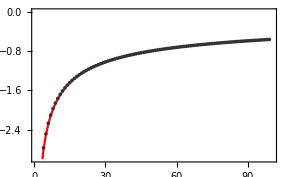

```mathematica
ClearAll[i1,z];

i1=Table[-c⟦2,k⟧*√(𝔻*(n-1)),{k,2,n}];
z=Table[-1./Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}];

ListPlot[{i1,z},
Joined->{False,True},
PlotRange -> {{1,n},{0,-3}},
PlotStyle->{Inherited,Red}]
```

Fig. Chapter.FigureCaption  Plot of analytical (line) and simulated (points) dimensionless currents.

### Chapter.Section.Subsection Functional methods

Functional methods in Mathematica offer significant computational speed improvements over procedural methods as we shall see below. An example of a functional version of the explicit solve method is:

```mathematica
ClearAll[explicitSolve2];

explicitSolve2[m_Integer,n_Integer, d_]:=Module[{𝔻=d,c},
c =makeGrid[m,n];
Map[Set[c⟦All,#⟧,Flatten[{c⟦1,#⟧,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},c⟦All,#-1⟧],c⟦m,#⟧}]]&,Range[2,n]]
]
```

In order to visualize how this works imagine that you had the following list {c_1^k, c_2^k, c_3^k, c_4^k, c_5^k, c_6^k} representing the concentrations at points on a grid. The calculation performed in the For loop in the earlier procedural method can be performed functionally using ListCorrelate.

```mathematica
ClearAll[𝔻,c,list,k];

list=Table[Subscript[c, j]^k,{j,1,6}];
ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},list]//TableForm
```

𝔻 c_1^k+(1-2 𝔻) c_2^k+𝔻 c_3^k
𝔻 c_2^k+(1-2 𝔻) c_3^k+𝔻 c_4^k
𝔻 c_3^k+(1-2 𝔻) c_4^k+𝔻 c_5^k
𝔻 c_4^k+(1-2 𝔻) c_5^k+𝔻 c_6^k

We can immediately see that the output, shown here in TableForm, is the explicit finite difference solution for c_2^(k+1), c_3^(k+1), c_4^(k+1), and c_5^(k+1). We could then add the boundary conditions eg. b1 and b2, on either side of the output and Flatten the list to create a single list of concentrations for the (k+1)th time increment.

```mathematica
Flatten[{b1,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},list],b2}]//TableForm
```

b1
𝔻 c_1^k+(1-2 𝔻) c_2^k+𝔻 c_3^k
𝔻 c_2^k+(1-2 𝔻) c_3^k+𝔻 c_4^k
𝔻 c_3^k+(1-2 𝔻) c_4^k+𝔻 c_5^k
𝔻 c_4^k+(1-2 𝔻) c_5^k+𝔻 c_6^k
b2

The output gives the concentration values c_1^(k+1), c_2^(k+1), c_3^(k+1), c_4^(k+1), c_5^(k+1), c_6^(k+1)at the k+1 time increment from the k time increment values used as input. The Set command is used to set the k+1 row on the grid as equal to the output. Next we want to look for an analogy to the For loop to do these steps for each value of k. In Mathematica this can be done with the Map function.
Placing the pure function Set[ … ]& in Map[…, Range[2, n]] is the functional equivalent to For[k = 2, k ≤ n, k++, … ]. Range[2, n] produces a list of values from 2 to n that are the values of k. Each successive value of k is mapped onto the function thereby producing the required output. Map is a short way of performing the following series of steps:

c⟦All,2⟧== Flatten[{c⟦1,2⟧,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},c⟦All,1⟧],c⟦m,2⟧}]

c⟦All,3⟧== Flatten[{c⟦1,3⟧,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},c⟦All,2⟧],c⟦m,3⟧}]

⋮

c⟦All,n⟧== Flatten[{c⟦1,n⟧,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},c⟦All,n-1⟧],c⟦m,n⟧}]

As we’ll see below the speed improvement in going from the procedural explicitSolve to the functional explicitSolve2 is not as great as we’d hoped. Below is a faster method called explicitSolve3.

```mathematica
Clear[explicitSolve3];

explicitSolve3[m_Integer,n_Integer, d_]:=Module[{solveNext,𝔻=d,c},
c =makeGrid[m,n];
c=Transpose[c];
solveNext[start_,{b1_,___,b2_}]:=Flatten[{b1,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},start],b2}];
c=FoldList[solveNext,First[c],Rest[c]];Rest[c]]
```

explicitSolve3 contains a function, solveNext. The function solveNext takes two lists as input variables. The variable start_ is a list of concentrations at a given value of k. The second variable, {b1_, ___, b2_}, is the row of grid points representing concentrations at a given value of k+1. The values b1 and b2 correspond to the first and last elements of the list that are in fact the boundaries of the grid at k+1. The three successive underscores, ___, stand for any sequence. All we are really interested in here is taking the first and last terms (the boundary values) at k+1 to use in the function. Using FoldList, solveNext is repeatedly applied to each element in the list Rest[c] beginning with the first row of concentrations (First[c]). For example for a list c={rowk1,rowk2,rowk3,rowk4} the function FoldList[solveNext, First[c], Rest[c]] is an abbreviated way of writing FoldList[solveNext, rowk1,{rowk2,rowk3,rowk4}].

```mathematica
FoldList[solveNext, rowk1,{ rowk2, rowk3, rowk3}]
```

{rowk1,solveNext[rowk1,rowk2],solveNext[solveNext[rowk1,rowk2],rowk3],solveNext[solveNext[solveNext[rowk1,rowk2],rowk3],rowk3]}

Applying solveNext to the initial concentrations at k=1 will return the concentrations at k=2. This output is then used as input for the next increment and the concentrations at k=3 are returned and so on until k=n. We Transpose the list at the beginning and end of explicitSolve3 solely to return output that has the same form in previous two explicitSolve methods. The final method, explicitSolve3 is considerably faster than the other two (Fig Chapter.FigureCaption). The relative computation times for the procedural and functional methods can be compared by wrapping the Timing command around the evaluation and executing the explicitSolve functions for list of n values. Below Map is used to insert successive n values from a list of values into the explicitSolve function.

```mathematica
ClearAll[𝔻,nValues,res1,res2];

𝔻=0.4;
nValues={100,200,400,600,800,1000};(*number of time increments*)
res1= Map[Timing[(
m=1+Ceiling[6*√(𝔻*(#-1))];
makeGrid[m,#];explicitSolve[m, #];)]&,nValues]
```

{{0.002922,Null},{0.005951,Null},{0.009739,Null},{0.012004,Null},{0.023421,Null},{0.02079,Null}}

```mathematica
res2=Map[Timing[(m=1+Ceiling[6*√(𝔻*(#-1))];
makeGrid[m,#];explicitSolve3[m, #];)]&,nValues]
```

{{0.003564,Null},{0.003855,Null},{0.007105,Null},{0.016535,Null},{0.018472,Null},{0.020334,Null}}

Null elements appear in the lists because a semicolon was placed after the explicitSolve functions to suppress the display of output (the complete list of concentrations on the grid). The output can be turned into a usable list for plotting by firstly flattening the list, then deleting all the Null elements and finally removing the units.

```mathematica
ClearAll[res1a,res1b,res2a,res2b];

res1a=DeleteCases[Flatten[res1],Null];
res2a=DeleteCases[Flatten[res2],Null];

(*make an x-y list containing timings and values of n*)
res1b=MapThread[{#1,#2}&,{nValues,res1a}];
res2b=MapThread[{#1,#2}&,{nValues,res2a}];
```

Alternatively the all of the first elements can be chosen from the list:

```mathematica
res1a=res1⟦All,1⟧;
res2a=res2⟦All,1⟧;

(*make an x-y list containing timings and values of n*)
res1b=Transpose@{nValues,res1a};
res2b=Transpose@{nValues,res2a};
```

Once the list of x-y {n, timing} points have been formed they can be plotted on a log plot.

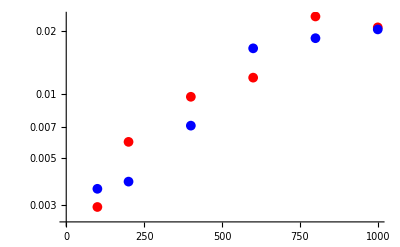

```mathematica
ListLogPlot[{res1b,res2b}, PlotStyle-> {Directive[Red,AbsolutePointSize[7]],Directive[Blue,AbsolutePointSize[7]]},Frame->False]
```

Fig. Chapter.FigureCaption  Plot of log of computation time versus n. Upper points are procedural timings and lower points are functional timings.

## Chapter.Section Implicit Finite Difference Methods

We can re-write eqn (Chapter.EquationNumbered) in a slightly different form so that the flux is calculated at the t + Δt time interval (Fig. Chapter.FigureCaption).

c(x, t+Δt)-c(x, t)=DΔt/(Δx)^2(c(x+Δx, t+Δt)-2c(x, t+Δt)+c(x-Δx, t+Δt))

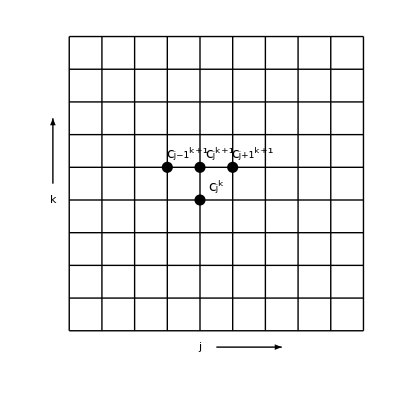

```mathematica
ClearAll[vert,horiz,option4,k,j,c];

vert=Table[Line[{{i,1},{i,10}}],{i,1,10}];
horiz=Table[Line[{{1,i},{10,i}}],{i,1,10}];

option4={
AspectRatio-> 1,
ImagePadding->{{5,5},{5,5}},
Prolog-> {
Text[TraditionalForm[k],{0.5,5.}],
Text[TraditionalForm[j],{5.,0.5}],
Text[label[Subscript[c, j]^k],{5.5,5.4}],
Text[label[Subscript[c, j]^(k+1)],{5.6,6.4}],
Text[label[Subscript[c, j-1]^(k+1)],{4.6,6.4}],
Text[label[Subscript[c, j+1]^(k+1)],{6.6,6.4}],
PointSize[0.02],
Point[{4,6}],
Point[{5,5}],
Point[{6,6}],
Point[{5,6}],
Arrowheads[{0,0.03}],
Arrow[{{0.5,5.5},{0.5,7.5}}],
Arrow[{{5.5,0.5},{7.5,0.5}}]
}
};

Graphics[{vert,horiz},PlotRange->{{0,10},{0,10}},option4]

SelectionMove[EvaluationNotebook[],Previous,Cell];
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell];
```

Fig. Chapter.FigureCaption  For the fully implicit method the concentration at time increment k is calculated from the concentration at time increment k+1.

Written in the coordinates of the grid eqn (Chapter.EquationNumbered) becomes

c(j, k+1)-c(j, k)=DΔt/(Δx)^2[c(j+1, k+1)-2c(j,k+1)+c(j-1, k+1)]

Using this equation the concentration at t=k can be determined from the concentration at t=k+1. This form of finite difference method is called a fully implicit or backward difference scheme. It is stable for all values of D. Written in dimensionless form eqn (Chapter.EquationNumbered) becomes

-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k

Equation (Chapter.EquationNumbered) can be written as a system of linear equations

-D c_1^(k+1)+(1+2D)c_2^(k+1)-D c_3^(k+1)=c_2^k
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
-D c_(m-2)^(k+1)+(1+2D)c_(m-1)^(k+1)-D c_m^(k+1)=c_(m-1)^k

that can be rearranged to give

(1+2D)c_2^(k+1)-D c_3^(k+1)=c_2^k+D c_1^(k+1)
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
-D c_(m-2)^(k+1)+(1+2D)c_(m-1)^(k+1)=c_(m-1)^k+D c_m^(k+1)

where the reader is reminded that c_1^(k+1)and c_m^(k+1)are boundary values. In matrix form the system of equations shown in (Chapter.EquationNumbered) is written as

((1+2D) | -D |   |   |   | 0
-D | (1+2D) | -D |   |   |  
  | -D | (1+2D) | -D |   |  
  |   | ⋱ | ⋱ | ⋱ |  
  |   |   | -D | (1+2D) | -D
0 |   |   |   | -D | (1+2D))·(c_2^(k+1)
c_3^(k+1)
⋮
c_j^(k+1)
⋮
c_(m-1)^(k+1))=(c_2^k+D c_1^(k+1)
c_3^k
⋮
c_j^k
⋮
c_(m-1)^k+D c_m^(k+1))

Equation (Chapter.EquationNumbered) is of the general form A·u=b. Matrix A has all its elements as zero except for elements on the main, super and subdiagonal and is known as a tridiagonal matrix, while u and b are referred to as column vectors.

## Chapter.Section Implicit Solution with Mathematica

Chapter.Section.Subsection Procedural method

To solve eqn (Chapter.EquationNumbered) in Mathematica we begin by making the diagonal, sub-diagonal, and super-diagonal elements of the matrix A. For a series of m distance points on a grid the resulting tridiagonal matrix is formed with m-2 rows.

```mathematica
ClearAll[makeDiagonals,m,α];

makeDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[-α,{m-3}];
		z=Table[-α,{m-3}];
		y=Table[1.+2.*α,{m-2}];
{x,y,z}
]
```

We can check that we have made the correct matrix

```mathematica
ClearAll[makeMatrix,x,y,z,𝔻];
makeMatrix[x_,y_,z_]:=Module[{n=Length[y]},SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},n]]

{x,y,z}=makeDiagonals[7,𝔻];
makeMatrix[x,y,z]//MatrixForm
```

(1.+2. 𝔻 | -𝔻 | 0 | 0 | 0
-𝔻 | 1.+2. 𝔻 | -𝔻 | 0 | 0
0 | -𝔻 | 1.+2. 𝔻 | -𝔻 | 0
0 | 0 | -𝔻 | 1.+2. 𝔻 | -𝔻
0 | 0 | 0 | -𝔻 | 1.+2. 𝔻)

Next step is to generate the vector b, which is the vector on the right hand side of eqn (Chapter.EquationNumbered), containing the concentrations at the kth time step. Here is a procedural method for implementing the solution.

```mathematica
ClearAll[implicitSolve1];

implicitSolve1[m_Integer,n_Integer,α_]:=Module[{k,j,b,x,y,z,soln,mat,c},
{x,y,z}=makeDiagonals[m,α];
mat=makeMatrix[x,y,z];
c=Table[1.,{m},{n}];
b=Table[1.,{m-2}];
For[k=2,k≤n,k++,
Module[{},
For[j=2,j≤m-1,j++,
c⟦1,k⟧=0.;
b⟦j-1⟧=c⟦j,k-1⟧
];
b⟦m-2⟧=b⟦m-2⟧+α;
soln=LinearSolve[mat,b];
For[j=2,j≤m-1,j++,c⟦j,k⟧=soln⟦j-1⟧]
]
];
c
]
```

```mathematica
soln1=With[{m=20,n=10,𝔻=1.5},
implicitSolve1[m,n,𝔻]
];

ListPlot3D[soln1,
AxesEdge->{{-1,-1},{1,-1},{1,1}}]
```

-Graphics3D-

### Chapter.Section.Subsection Functional methods

The first step in writing an implicit method is to write a function called SolveNext to solve eqn (Chapter.EquationNumbered) at each time step.

```mathematica
ClearAll[solveNext];

solveNext[mat_,α_]:=Module[{tmp,b},
tmp=#⟦2;;-2⟧;
b=Flatten[{tmp⟦1;;-2⟧,Last[tmp]+α}];
Flatten[{0.,LinearSolve[mat,b],1.}]
]&
```

```mathematica
With[{mat=makeMatrix[20,1.5],b=Table[1.,{20}]},solveNext[mat,1.5][b]]
```

{0.,LinearSolve[makeMatrix[20,1.5],{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.5}],1.}

solveNext begins by making a list, called tmp, by dropping the first and last terms, which are the boundary values, from a list of concentrations. The first and last values of list tmp now correspond to c_2^(k+1)and c_(m-1)^(k+1)respectively. In this example, for a potential step to the limiting current region, c_1^(k+1)=0 so that c_2^k+D c_1^(k+1)=c_2^k. Since c_m^(k+1)=1, c_(m-1)^k+D c_m^(k+1)=c_(m-1)^k+D which is written as Last[tmp]+𝔻. A new list, b, is thus created that corresponds to the vector b in eqn (Chapter.EquationNumbered). The final step in solveNext is to solve the tridiagonal matrix using the matrix solver LinearSolve, and add the new boundary values to produce a list of concentrations at k+1. LinearSolve[A,b] solves a system of linear equations of the form A·u=b. NestList is used to apply solveNext to successive rows of concentrations beginning with the initial concentrations.

```mathematica
ClearAll[implicitSolve2];

implicitSolve2[m_Integer,n_Integer,α_]:=Module[{x,y,z,solveNext,mat,b1},

{x,y,z}=makeDiagonals[m,α];
mat=makeMatrix[x,y,z];
b1=ConstantArray[1.,{m}];
solveNext[mat1_,α1_]:=Module[{tmp,b},
tmp=#⟦2;;-2⟧;
b=Flatten[{tmp⟦1;;-2⟧,Last[tmp]+α1}];
Flatten[{0.,LinearSolve[mat1,b],1.}]
]&;

Transpose@NestList[solveNext[mat,α],b1,n-1]
]
```

```mathematica
soln2=implicitSolve2[20,10,1.5];
ListPlot3D[soln2,AxesEdge->{{-1,-1},{1,-1},{1,1}}]
```

-Graphics3D-

NestList is a function that applies solveNext repeatedly with the output from the kth step becoming the input for the (k+1)th step. Applying solveNext to the initial concentrations at k=1 will return the concentrations at k=2. This output is then used as input for the next increment and the concentrations at k=3 are returned and so on until k=n. Finally the list of concentrations are transposed to allow comparison with the procedural method.

Typical computation times for the four implicit methods can be determined and plotted in the same way as described in §2.5.2.

```mathematica
ClearAll[n,m,𝔻,c,initial,nValues];

𝔻=1.5;(*model diffusion coefficient*)
nValues={100,200,400,600,800,1000};
```

```mathematica
(*procedural method*)
res3= Map[Timing[(m=1+Ceiling[6*√(𝔻*(#-1))];implicitSolve1[m, #,𝔻];)]&,nValues]
```

{{0.239309,Null},{0.626406,Null},{1.02735,Null},{1.41942,Null},{1.90657,Null},{2.41584,Null}}

```mathematica
(*LinearSolve method*)
res4= Map[Timing[(m=1+Ceiling[6*√(𝔻*(#-1))];implicitSolve2[m, #,𝔻];)]&,nValues]
```

{{0.010744,Null},{0.113012,Null},{0.234266,Null},{0.409977,Null},{0.719134,Null},{0.78652,Null}}

The timings are converted into a plotable list by firstly flattening the list, then deleting all the Null elements and finally removing the units.

```mathematica
res3a=Transpose[{nValues,res3⟦All,1⟧}];

res4a=Transpose[{nValues,res4⟦All,1⟧}];
```

The relative calculation times are shown in Fig. Chapter.FigureCaption. The sharp increase in computation time when using LinearSolve is due to the increasing computation time with increasing matrix size. The size of the matrix diagonals is m-2 whereas the matrix size is (m-2)^2. This is not such a problem when using LUDecomposition since the matrix decomposition is performed only once.

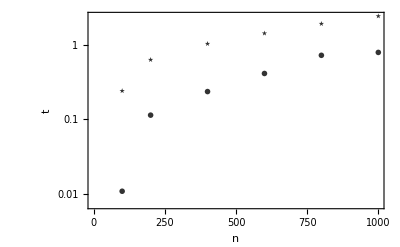

```mathematica
ListLogPlot[{res3a,res4a},options2]
```

Fig. Chapter.FigureCaption  Plot of computation time versus n for a potential step to the limiting current region. implicitSolve1(★),implicitSolve2(•).

## Chapter.Section Summary

In this chapter explicit and implicit finite difference methods were introduced and examples of the use of Mathematica to solve the finite difference equations for a potential to a limiting current region were given. In the next chapter methods to improve the accuracy of the results by combining both the explicit and implicit methods and enhance the computation speed by using an expanding grid are examined.

## Further Reading

Britz, D. (1988). Digital Simulation in Electrochemistry, Springer-Verlag, Berlin.
Feldberg, S. W. (1969). Digital Simulation: A General Method for Solving Electrochemical Diffusion-Kinetic Problems. In Electroanalytical Chemistry, Vol. 3. (ed. A. J. Bard), pp. 199-296. Marcel Dekker, New York.
Press, W. H., Teukolsky, S. A., Vetterling, W. T., and Flannery, B. P. (1992). Numerical Recipes in C, (2nd edn). Chapter 19. Cambridge University Press, New York.
Richtmyer, R. D. and Morton, K. W. (1967). Difference Methods for Initial Value Problems, (2nd edn) Wiley, New York.
Speiser, B. (1996). Numerical Simulation of Electroanalytical Experiments: Recent Advances in Methodology. In Electroanalytical Chemistry, Vol. 19. (ed. A. J. Bard and I. Rubenstein), pp. 1-109. Marcel Dekker, New York.
Wolfram, S. (1999). The Mathematica Book, (4th edn) Cambridge University Press/Wolfram Media, New York/Champaign.
Wolfram Research (1999). Mathematica 4 Standard Add-on Packages, (4th edn). Wolfram Media, Champaign.